```mathematica
(*PROBLEM 2 D*)
ClearAll["Global`*"]
rhoconvert:=7.425*10^-19;
Pconvert:=8.261*10^-40;
K:=7.32;
rho0c:=7.425*10^-4;
rho[r]:=(Pres[r]/K)^(3/5)+1.5*Pres[r];
eq1=D[m[r],r]==4*π*rho[r]*r^2;  (*added term here*)
eq2=D[Pres[r],r]==-((rho[r]+Pres[r])*(m[r]+4*π*r^3*Pres[r]))/(r*(r-2*m[r]));
eq3=D[mp[r],r]==4*π*rho[r]*r^2*(1-(2*m[r])/r)^(-1/2)
bc1=m[10^-100]==0;      (*To avoid 0 denominator*)
bc2=Pres[10^-100]==K*rho0c^(5/3);
bc3=mp[10^-100]==0;   (*The same boundary condition as for m*)
```

mp'[r]==(4 π r^2 (0.302896 Pres[r]^(3/5)+1.5 Pres[r]))/(√(1-(2 m[r])/r))

```mathematica
sol=NDSolve[{eq1,eq2,eq3,bc1,bc2,bc3},{m,Pres,mp},{r,10^-100,16}]
```

{{m→InterpolatingFunction[{{1.×10^-100,16.}},<>],Pres→InterpolatingFunction[{{1.×10^-100,16.}},<>],mp→InterpolatingFunction[{{1.×10^-100,16.}},<>]}}

```mathematica
m[r_]=m[r]/.sol;
Pres[r_]=Pres[r]/.sol;
mp[r_]=mp[r]/.sol;
```

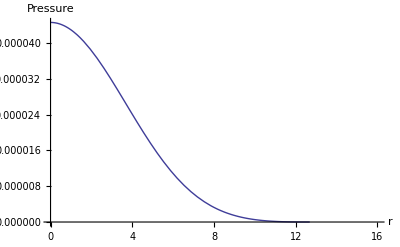

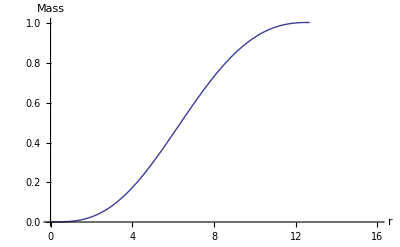

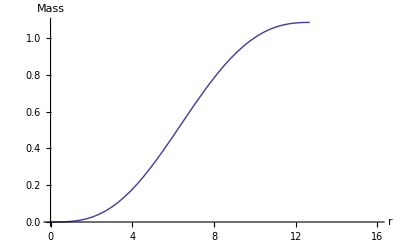

```mathematica
Plot[Pres[r],{r,10^-100,16},AxesLabel->{r,Pressure},AxesOrigin->{0,0}]
Plot[m[r],{r,10^-100,16},AxesLabel->{r,Mass},AxesOrigin->{0,0}]
Plot[mp[r],{r,10^-100,16},AxesLabel->{r,Mass},AxesOrigin->{0,0}]
```

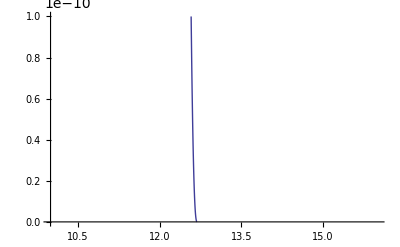

```mathematica
(*Now zoom into graph of Pressure to see where it approaches 0*)
Plot[Pres[r],{r,10,16},PlotRange->{0,10^-10}]
```

```mathematica
(*The approximate radius where pressure now vanishes is about 12.8 and since we are not asked to give the exact radius the value 12.8 which is larger than the real value is sufficient as mathematica will still give the same result for mp. The programme just gives the same value after it has really gone to 0 *)
```

```mathematica
(*Get the desired mass at radius 12.8*)
Re[Evaluate[mp[12.8]]]
```

{1.0852}